# 2 - Particles Configuration

```mathematica
CGcoeff[J1_,J2_,J_]:=ThreeJSymbol[J1,J2,{J[[1]],-J[[2]]}](-1)^(-J1[[1]]+J2[[1]]-J[[2]])√(2J[[1]]+1)
```

```mathematica
TableForm[Table[(2n)^2/2 CGcoeff[{(2n-1)/2,1/2},{(2n-1)/2,-1/2},{j,0}]^2//N,{n,1,7},{j,0,2n-1,2}],
TableHeadings->{Table[(2m1-1)/2,{m1,1,7,1}],Table[m2,{m2,0,9,2}]}]
```

| 0 | 2 | 4 | 6 | 8 |  | 
1/2 | 1. |  |  |  |  |  | 
3/2 | 2. | 2. |  |  |  |  | 
5/2 | 3. | 3.42857 | 2.57143 |  |  |  | 
7/2 | 4. | 4.7619 | 4.20779 | 3.0303 |  |  | 
9/2 | 5. | 6.06061 | 5.66434 | 4.84848 | 3.42657 |  | 
11/2 | 6. | 7.34266 | 7.04895 | 6.41711 | 5.41038 | 3.7809 | 
13/2 | 7. | 8.61538 | 8.39654 | 7.88066 | 7.08502 | 5.91793 | 4.10446

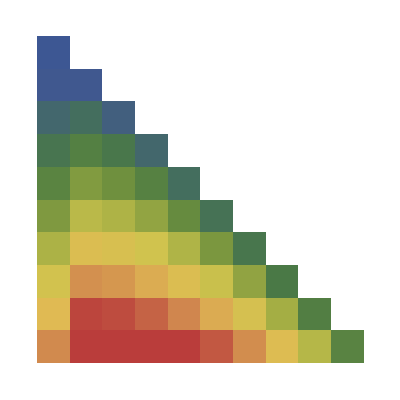

```mathematica
ArrayPlot[Table[(2n)^2/2 CGcoeff[{(2n-1)/2,1/2},{(2n-1)/2,-1/2},{j,0}]^2,{n,1,10},{j,0,2n-1,2}],ColorFunction->"DarkRainbow"]
```

```mathematica
A[V0_,V1_,p1_,p2_,J_]:=Module[{lp,sp,jp,ln,sn,jn,T, Tz},
Tz=p1[[3]]+p2[[3]];
If[p1[[3]]==1/2 && p2[[3]]==-1/2,lp=p1[[1]];sp=p1[[2]];ln=p2[[1]];sn=p2[[2]];T=3];
If[p1[[3]]==-1/2 && p2[[3]]==+1/2,lp=p2[[1]];sp=p2[[2]];ln=p1[[1]];sn=p1[[2]];T=3];
If[p1[[3]]== p2[[3]],lp=p1[[1]];sp=p1[[2]];ln=p2[[1]];sn=p2[[2]];T=1;];
If[lp==0 ,jp=Abs[sp],jp=lp+sp];
If[ln==0,jn=Abs[sn],jn=ln+sn];
If[MemberQ[Table[i,{i,Abs[jp-jn],jp+jn,1}],J],
If[Mod[lp+ln-J,2]==0 && T==1,
(2jp+1)(2jn+1)CGcoeff[{jp,1/2},{jn,-1/2},{J,0}]^2,
If[T==3 && J≠0,
(2jp+1)(2jn+1)CGcoeff[{jp,1/2},{jn,-1/2},{J,0}]^2(V0 (1+Power[-1,lp+ln+J])/2+V1((1-Power[-1,lp+ln+J])/2+((2 jp+1)+Power[-1,jp+jn+J](2jn+1))^2/(4J(J+1))))
,0]
,0]
,0]
]
```

```mathematica
Manipulate[
Module[{j1,j2},
j1=If[l1==0 ,Abs[s1],l1+s1];
j2=If[l2==0 ,Abs[s2],l2+s2];
TableForm[
Table[
{j1,j2,
A[1,2,{l1,s1,t1},{l2,s2,t2},J]//N},{J,Abs[j1-j2],j1+j2,1}],
TableHeadings->{
Table[J,{J,Abs[j1-j2],j1+j2,1}],
{"j1","j2","A"}
}]
],
{l1,0,6,1,Appearance-> "Labeled"},
{s1,{-1/2,1/2}},{t1,{-1/2,1/2}},
{l2,0,6,1,Appearance-> "Labeled"},
{s2,{-1/2,1/2}},{t2,{-1/2,1/2}},
ContinuousAction->False
]
```

```mathematica
Manipulate[Module[{j1,j2},
j1=If[l1==0,l1+1/2,l1+s1];
j2=If[l2==0,l2+1/2,l2+s2];
CGTable=Table[
If[Mod[l1+l2-j,2]==0,
Re[CGcoeff[{j1,1/2},{j2,-1/2},{j,0}]]^2(2j1+1)(2j2+1)//N
,0]
,{j,Abs[j1-j2],j1+j2,1}];
TableForm[CGTable,TableHeadings->{Table[j,{j,Abs[j1-j2],j1+j2,1}]}]
],
{l1,0,6,1,Appearance-> "Labeled"},
{s1,{-1/2,1/2}},
{l2,0,6,1,Appearance-> "Labeled"},
{s2,{-1/2,1/2}},
ContinuousAction->False]
```